# Sample trajectories for an eccentric binary with backreaction in the low velocity limit

## Mass values and distance from detector

```mathematica
m1=Mean[{1.36,2.26}]*10^30;
m2=Mean[{0.86,1.36}]*10^30;
M=m1+m2
μ=(m1*m2)/M
δ=M/(4μ)
f1=m2/M;f2=m1/M;
G=6.67*^-11;c=3*^8;
Rst=(4 G^3 μ M^2/c^6)^(1/3)
z=(40*^6)*(3.1*^16)
```

2.92×10^30

6.88048×10^29

1.06097

2121.77

1.24×10^24

## Nondimensionalized radiation reaction equations

```mathematica
aeqn=a'[τ]==-16/5 a[τ]^-3(1-e[τ]^2)^(-7/2)(1+(73 e[τ]^2)/24+(37 e[τ]^4)/96);
eeqn=e'[τ]==-76/15 a[τ]^-4(1-e[τ]^2)^(-5/2)e[τ](1+(121 e[τ]^2)/304);
```

Initial values of semi-latus rectum and eccentricity are a(0)=50, e(0)=0.8.

```mathematica
a0=50;e0=0.8;tmax=10^6;tend=tmax;
sol=NDSolve[{aeqn,eeqn,a[0]==a0,e[0]==e0,WhenEvent[Chop[a'[τ]]==0||Chop[e'[τ]]==0,tend=τ;"StopIntegration"]},{a,e},{τ,0,tmax},WorkingPrecision->20,MaxSteps->Infinity];
```

NDSolve::precw: The precision of the differential equation ({{a'[τ]==-(16 (1+73/24 e[«1»]^2+37/96 e[«1»]^4))/(5 a[τ]^3 (1-Power[«2»])^(7/2)),e'[τ]==-(76 e[τ] (1+121/304 e[«1»]^2))/(15 a[τ]^4 (1-Power[«2»])^(5/2)),a[0]==50,e[0]==0.8},{},{},{},{WhenEvent[Chop[a'[τ]]==0||Chop[e'[τ]]==0,tend=τ;StopIntegration]}}) is less than WorkingPrecision (20.).

NDSolve::ndsz: At τ == 14187.109558413809947, step size is effectively zero; singularity or stiff system suspected.

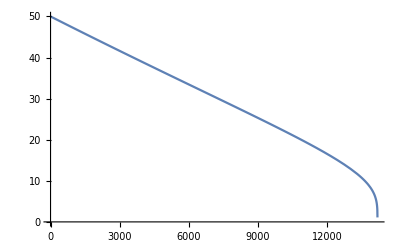

```mathematica
Plot[a[τ]/.First@sol,{τ,0,14187}]
```

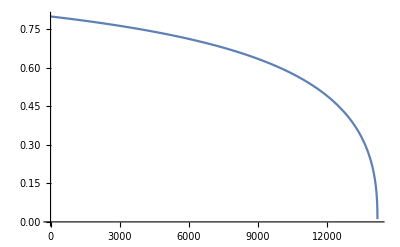

```mathematica
Plot[e[τ]/.First@sol,{τ,0,14187}]
```

```mathematica
Animate[ParametricPlot[{(a[τ](1-e[τ]^2))/(1+e[τ]Cos[δ^(1/6)a[τ]^(-3/2)τ])Cos[δ^(1/6)a[τ]^(-3/2)τ],(a[τ](1-e[τ]^2))/(1+e[τ]Cos[δ^(1/6)a[τ]^(-3/2)τ])Sin[δ^(1/6)a[τ]^(-3/2)τ]}/.First@sol,{τ,tanim-500,tanim},PlotPoints->500,PlotRange->{{-55,15},{-30,30}}],{tanim,2000,14180,5}]
```

```mathematica
Animate[ParametricPlot[{{(f1*a[τ](1-e[τ]^2))/(1+e[τ]Cos[δ^(1/6)a[τ]^(-3/2)τ])Cos[δ^(1/6)a[τ]^(-3/2)τ],(f1*a[τ](1-e[τ]^2))/(1+e[τ]Cos[δ^(1/6)a[τ]^(-3/2)τ])Sin[δ^(1/6)a[τ]^(-3/2)τ]}/.First@sol,{(-f2*a[τ](1-e[τ]^2))/(1+e[τ]Cos[δ^(1/6)a[τ]^(-3/2)τ])Cos[δ^(1/6)a[τ]^(-3/2)τ],(-f2*a[τ](1-e[τ]^2))/(1+e[τ]Cos[δ^(1/6)a[τ]^(-3/2)τ])Sin[δ^(1/6)a[τ]^(-3/2)τ]}/.First@sol},{τ,tanim-500,tanim},PlotPoints->500,PlotRange->{{-30,50},{-30,30}},PlotStyle-> {Directive[Red,Small],Directive[Blue,Small]}],{tanim,2000,14180,5}]
```

## Plotting the waveforms

```mathematica
Q=((a[τ](1-e[τ]^2))/(1+e [τ]Cos[δ^(1/6)a[τ]^(-3/2) τ]))^2{{Cos[δ^(1/6)a[τ]^(-3/2) τ]^2,Sin[δ^(1/6)a[τ]^(-3/2) τ]Cos[δ^(1/6)a[τ]^(-3/2) τ]},{Sin[δ^(1/6)a[τ]^(-3/2) τ]Cos[δ^(1/6)a[τ]^(-3/2) τ],Sin[δ^(1/6)a[τ]^(-3/2) τ]^2}};
Qddot=D[Q,{τ,2}];
```

```mathematica
hp[τ_]:=G/(z c^4)*(Qddot⟦1,1⟧-Qddot⟦2,2⟧)/.First@sol;
hx[τ_]:=(2G)/(z c^4)*Qddot⟦1,2⟧/.First@sol;
```

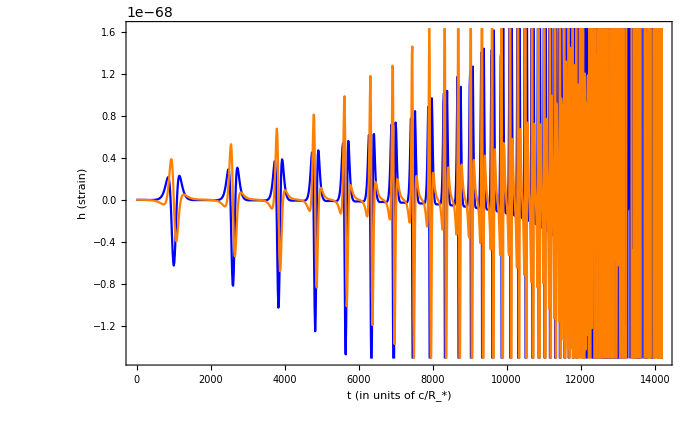

```mathematica
waveplot=Plot[{hp[τ],hx[τ]},{τ,0,14180},PlotStyle->{Blue,Orange},PlotPoints->1000,ImageSize->700,Frame-> True,FrameLabel->{Style["t (in units of c/R_*)",16],Style["h",Italic,16]Style[" (strain)",16]},LabelStyle->Directive[Bold, Medium]]
```

## Exporting to a video

This line of code exports an animation of the binary orbiting around each other undergoing orbital decay. The video file is an .avi file and it is exported to Directory[].

```mathematica
Clear[frames];numFrames=400;tRange=Subdivide[0,14180,numFrames-1];frames=ConstantArray[0,Length[tRange]];
```

```mathematica
x1[τ_]:=(f1*a[τ](1-e[τ]^2))/(1+e[τ]Cos[δ^(1/6)a[τ]^(-3/2)τ])Cos[δ^(1/6)a[τ]^(-3/2)τ]/.First@sol;
y1[τ_]:=(f1*a[τ](1-e[τ]^2))/(1+e[τ]Cos[δ^(1/6)a[τ]^(-3/2)τ])Sin[δ^(1/6)a[τ]^(-3/2)τ]/.First@sol;
x2[τ_]:=(-f2*a[τ](1-e[τ]^2))/(1+e[τ]Cos[δ^(1/6)a[τ]^(-3/2)τ])Cos[δ^(1/6)a[τ]^(-3/2)τ]/.First@sol;
y2[τ_]:=(-f2*a[τ](1-e[τ]^2))/(1+e[τ]Cos[δ^(1/6)a[τ]^(-3/2)τ])Sin[δ^(1/6)a[τ]^(-3/2)τ]/.First@sol;
```

```mathematica
For[k=1,k≤numFrames,k++,
tk=tRange⟦k⟧;
x1k=x1[tk];
y1k=y1[tk];
x2k=x2[tk];
y2k=y2[tk];

frames⟦k⟧=GraphicsGrid[{{Show[
ParametricPlot[{x1[t],y1[t]},{t,Max[0,tk-100],Max[0.1,tk]},PlotRange->{{-35,55},{-30,30}},PlotStyle->Thickness[0.008],ColorFunction->Function[{x,y,w},Opacity[w,Red]],Frame-> True,GridLines->Automatic,ImageSize->500,FrameLabel->"t = "<>ToString[Rst/c*tk],LabelStyle->Directive[Bold, Medium]],
ParametricPlot[{x2[t],y2[t]},{t,Max[0,tk-100],Max[0.1,tk]},PlotRange->{{-35,55},{-30,30}},PlotStyle->Thickness[0.008],ColorFunction->Function[{x,y,w},Opacity[w,Blue]],Frame-> True,GridLines->Automatic,ImageSize->500,FrameLabel->"t = "<>ToString[Rst/c*tk],LabelStyle->Directive[Bold, Medium]],
Graphics[{AbsolutePointSize[10],Red,Point[{x1k,y1k}]}],
Graphics[{AbsolutePointSize[10],Blue,Point[{x2k,y2k}]}]
]},{Show[waveplot,ImageSize-> 500,
Epilog->{Inset[Graphics[{Thick,Red,Line[{{1,-10},{1,10}}]},ImageSize->50],{tRange⟦k⟧,0}],
Inset[Framed[Column[{
LineLegend[{Blue}, {"h_+"}],
LineLegend[{Orange}, {"h_x"}]
}],RoundingRadius->5,Background->White],{1200,1.25*^-68}]}]}},Frame->All
]

]
Export["SampleGWTrajectory.avi",frames]
```

SampleGWTrajectory.avi

```mathematica
Directory[]
```

E:\Joshua\Documents

## The “sound” of the gravitational wave

```mathematica
Clear[amps,samples,soundfun]
```

```mathematica
soundfun[τ_]=G/(z c^4)*(Qddot⟦1,1⟧-Qddot⟦2,2⟧)/.First@sol;
```

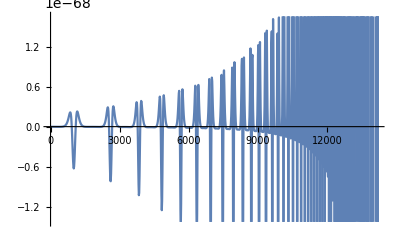

```mathematica
Plot[soundfun[t],{t,0,14180},PlotPoints->1000]
```

```mathematica
samples=Subdivide[0,14180,4999];
```

```mathematica
amps=Table[soundfun[i],{i,samples}];
```

```mathematica
ts=TimeSeries[amps,{samples}];
```

```mathematica
ListPlay[ts,SampleRate->8000]
```

-Graphics-